```mathematica
<<Units`
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### Mass m, kinetic energy ϵ incident on a target M

```mathematica
Solve[ReplaceAll[(γ-1)m==ϵ,γ->1/Sqrt[1-β^2]],β]
```

{{β→-(√ϵ √(2 m+ϵ))/(m+ϵ)},{β→(√ϵ √(2 m+ϵ))/(m+ϵ)}}

#### Rutherford cross section for energy loss Ed (classical, spin-0 and spin-1/2)

```mathematica
rutherford=(2Pi α^2 Z^2)/(M β^2 Ed^2);
rutherford0=(2Pi α^2 Z^2)/(M β^2 Ed^2)(1-β^2 Ed/ekin);
```

#### For simple rutherford xc, dE/dx is purely logarithmic

```mathematica
Integrate[rutherford*n*Ed,{Ed,emin,emax},Assumptions->{Ed>0,emin>0,emax>emin}]
```

(2 n π Z^2 α^2 Log[emax/emin])/(M β^2)

```mathematica
SP=(2n π Z^2 α^2 Log[(emax/emin)])/(M β^2);
```

```mathematica
SP0=Integrate[rutherford0*n*Ed,{Ed,emin,emax},Assumptions->{Ed>0,emin>0,emax>emin}]/.ekin->Ekin;
```

```mathematica
SPpauli=Integrate[rutherford0*npaulirel*Ed,{Ed,emin,emax},Assumptions->{Ed>0,emin>0,emax>emin}]/.ekin->Ekin;
```

#### Scattering off Degenerate Targets, Fermi Energy Ef

```mathematica
npaulirel:=Integrate[e^2/Pi^2,{e,Ef-Ed,Ef}]
```

```mathematica
Convert[10^33 Centimeter^-3*(200 Mega ElectronVolt*Fermi)^3,(Mega ElectronVolt)^3]
```

8 ElectronVolt^3 Mega^3

```mathematica
ReplaceAll[npaulirel,Ed->Ef]
```

Ef^3/(3 π^2)

```mathematica
(3 Pi^2 n)^(1/3)/.n->8
```

2 3^(1/3) π^(2/3)

```mathematica
plotrel=Plot[ReplaceAll[npaulirel,{Ef->2 3^(1/3) π^(2/3),n->8}],{Ed,0,2 3^(1/3) π^(2/3)}];naiveplot=Plot[ReplaceAll[n*(Ed/Ef),{Ef->2 3^(1/3) π^(2/3),n->8}],{Ed,0,2 3^(1/3) π^(2/3)}];
```

#### Compare effective number density with naive Pauli-blocking factor - upper end of plot is Ef

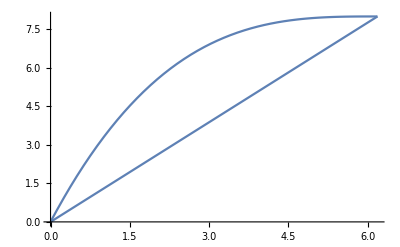

```mathematica
Show[plotrel,naiveplot]
```

#### Coulomb Log Emax

```mathematica
collision[b_]:=(2 Z^2 α^2)/(M b^2 β^2)
```

```mathematica
Ekin=(2M β^2 γ^2)/(1+2γ (M/m)+(M/m)^2);
```

#### Coulomb Log Emin

```mathematica
λTF=((6Pi Z α n)/Ef)^(-1/2);
```

```mathematica
Esc=collision[λTF]
```

(12 n π Z^3 α^3)/(Ef M β^2)

```mathematica
λTF/.{Z->6,α->1/137,Ef->0.5,n->0.8}
```

0.87011

```mathematica
Elattice:=(Z^2 α)/(n/Z)^(-1/3)
```

#### SP in units of MeV/(10^-5 cm)

```mathematica
Convert[(Mega ElectronVolt)^2 1/(200 Mega ElectronVolt*Fermi),(Mega ElectronVolt)/Centimeter]//N
```

(5.×10^10 ElectronVolt Mega)/Centimeter

#### Stopping power due to Coulomb Collisions off carbon nuclei

```mathematica
dedx:=ReplaceAll[ReplaceAll[ReplaceAll[ReplaceAll[1/Z SP,{emin->Max[Esc,Elattice],emax->Ekin}],Ef->(3 Pi^2 n)^(1/3)],γ->1/Sqrt[1-β^2]],β->(√ϵ √(2 m+ϵ))/(m+ϵ)];
```

```mathematica
electron=LogLogPlot[ReplaceAll[ReplaceAll[dedx 5.*^5,{α->1/137,M->12000,Z->6,n->0.8}],m->0.511],{ϵ,10^-2,10^7},PlotLegends->{"Coulomb (nuclei)"},PlotStyle->{Blue,Thick}];
```

```mathematica
electronflat=LogLogPlot[ReplaceAll[ReplaceAll[dedx 5.*^5,{α->1/137,M->12000,Z->6,n->0.8}],m->0.511]/.ϵ->10^7,{x,10^7,10^10},PlotStyle->{Thick,Blue}];
```

```mathematica
test=LogLogPlot[3.166286988823056/k^2,{k,1,10^3}];
```

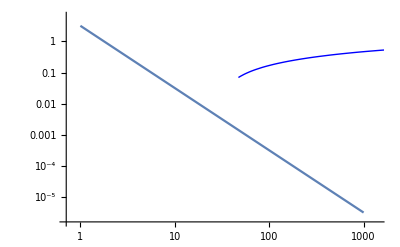

```mathematica
Show[test,electron]
```

```mathematica
pion=LogLogPlot[ReplaceAll[ReplaceAll[dedx 5.*^5,{α->1/137,M->12000,Z->6,n->8}],m->140],{ϵ,10^-1,10^10},PlotLegends->{"Coulomb (nuclei)"},PlotStyle->{Blue,Thick}];
```

```mathematica
proton=LogLogPlot[ReplaceAll[ReplaceAll[dedx 5.*^5,{α->1/137,M->12000,Z->6,n->8}],m->1000],{ϵ,10^-1,10^10},PlotLegends->{"Coulomb (nuclei)"},PlotStyle->{Blue,Thick}];
```

#### Stopping power due to Coulomb Collisions off Electrons

```mathematica
electronpauliflat=LogLogPlot[ReplaceAll[ReplaceAll[ (dedxpaulinondeg+dedxpaulidegelectron[10^7]) 5.*^5,{α->1/137,M->0.511,Z->1,n->0.8}],m->0.511]/.ϵ->10^7,{x,10^7,10^10},PlotStyle->{Orange,Thick}];
```

```mathematica
electronpauli=LogLogPlot[ReplaceAll[ReplaceAll[ (dedxpaulinondeg+dedxpaulidegelectron[ϵ]) 5.*^5,{α->1/137,M->0.511,Z->1,n->0.8}],m->0.511],{ϵ,10^-1,10^7},PlotLegends->{"Coulomb (electron)"},PlotStyle->{Orange,Thick}];
```

```mathematica
pionpauli=LogLogPlot[ReplaceAll[ReplaceAll[(dedxpaulinondeg+dedxpaulideg) 5.*^5,{α->1/137,M->0.511,Z->1,n->8}],m->140],{ϵ,10^-1,10^10},PlotLegends->{"Coulomb (electron)"},PlotStyle->{Orange,Thick}];
```

```mathematica
protonpauli=LogLogPlot[ReplaceAll[ReplaceAll[(dedxpaulinondeg+dedxpaulideg) 5.*^5,{α->1/137,M->0.511,Z->1,n->8}],m->1000],{ϵ,10^-1,10^10},PlotLegends->{"Coulomb (electron)"},PlotStyle->{Orange,Thick}];
```

#### Just examine the Coulomb Logarithm, find where scattering should “shut off” for protons and pions.

```mathematica
coulomblog={Max[Esc,Elattice],Ekin}/.{Ef->(3 Pi^2 n)^(1/3)}/.{γ->1/Sqrt[1-β^2]}/.{β->(√ϵ √(2 m+ϵ))/(m+ϵ)}/.{α->1/137,M->12000,Z->6,n->0.8};
```

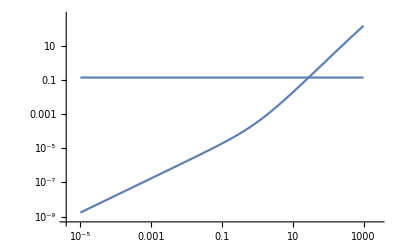

```mathematica
LogLogPlot[coulomblog/.m->0.511,{ϵ,0.00001,10^3}]
```

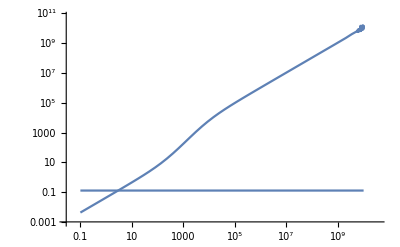

```mathematica
LogLogPlot[coulomblog/.m->140,{ϵ,0.1,10^10}]
```

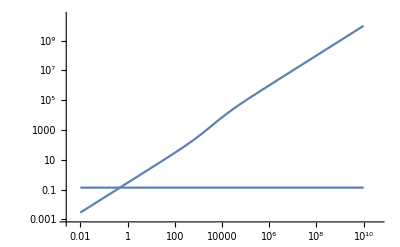

```mathematica
LogLogPlot[coulomblog/.m->1000,{ϵ,0.01,10^10}]
```

```mathematica
dedxpaulideg:=ReplaceAll[ReplaceAll[ReplaceAll[ReplaceAll[SPpauli,{emin->Esc,emax->Min[Ekin,Ef]}],Ef->(3 Pi^2 n)^(1/3)],γ->1/Sqrt[1-β^2]],β->(√ϵ √(2 m+ϵ))/(m+ϵ)];
```

```mathematica
dedxpaulidegelectron[ϵ_]:=If[ϵ>(3 Pi^2 n)^(1/3)/.n->0.8,dedxpaulideg/.{α->1/137,M->0.511,Z->1,n->0.8}/.m->0.511,0];
```

```mathematica
dedxpaulinondeg:=ReplaceAll[ReplaceAll[ReplaceAll[ReplaceAll[ReplaceAll[1/Z SP0,emin->Min[Ef,Ekin]],emax->Ekin],Ef->(3 Pi^2 n)^(1/3)],γ->1/Sqrt[1-β^2]],β->(√ϵ √(2 m+ϵ))/(m+ϵ)];
```